39

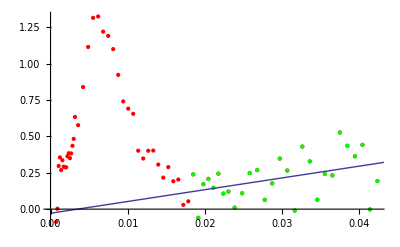

{-0.0283836+8.09145 x, | Estimate | Standard Error | t-Statistic | P-Value
a | 8.09145 | 3.57786 | 2.26154 | 0.0323191
b | -0.0283836 | 0.109104 | -0.260151 | 0.796797}

```mathematica
prefix = "PET-";
sample = "215";
path = ParentDirectory[NotebookDirectory[]] <> "/data/" <> prefix <> sample;
rawData=Import[path<>".0.phg","Table"];

data = Take[rawData, -(Length[rawData]-7)];

toRel[array_] := {array[[1]]/(2*Pi), array[[2]]*(array[[1]] /(2*Pi))^2};
rel = Map[toRel, data];

sample = 28;
notSample = Length[data ] - sample;

linearData =  Take[rel, -sample];
nonLinearData = Take[rel, Length[data ] - sample];
lFit = NonlinearModelFit[linearData,a x + b,{a,b},{x}];
Show[ListPlot[rel,PlotStyle->Red], ListPlot[linearData,PlotStyle->Green],Plot[{lFit["BestFit"]},{x,0,0.044}]]

lFit[{"BestFit","ParameterTable"}]

Export[path<>".rel", rel, "Table"];
Export[path <> ".fit", lFit, "String"];
Export[path<>"-fitPoints.rel", linearData, "Table"];
Export[path<>"-nonFitPoints.rel", nonLinearData, "Table"];
```